# Forward Euler, Forward Euler with Corrector method

```mathematica
u0 = 1;
a=2;
x0=0;
dx = .1;
u[x_]:= E^x;
up[x_]:= a*x;
```

```mathematica
ucomp = {};
uact = {};
uerror = {};
For[i = 0, i ≤ 9, i++, 
(* compute and append actual value *)
act = u[a*i*dx];
AppendTo[uact,act];
(* append computed value *)
AppendTo[ucomp,u0];
(* compute and append error *)
err = Abs[act - u0];
AppendTo[uerror,err];
(*compute actual *)
u0 = u0 + up[u0]*dx;
];
Print["computed"]
ucomp
Print["actual"]
uact
Print["uerror"]
uerror
```

computed

{1,1.2,1.44,1.728,2.0736,2.48832,2.98598,3.58318,4.29982,5.15978}

actual

{1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965}

uerror

{0.,0.0214028,0.0518247,0.0941188,0.151941,0.229962,0.334133,0.472019,0.653215,0.889867}

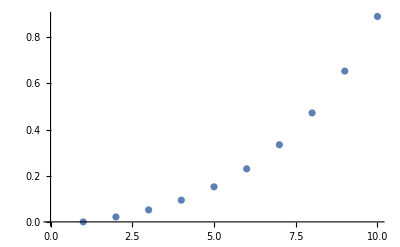

```mathematica
ListPlot[uerror]
```

```mathematica
(* CORRECTOR 
now we want the following:   

we use x0 and u0 to compute a value of the derivative up[u0], we can use up[u1] where we have just computed u1 to recalculate our estimate for up[u0]. 

set upcorrected = Avg(up[u0] and u[u1]). Then recompute u1.  

*)
```

```mathematica
u0 = 1;
a=2;
x0=0;
dx = .1;
u[x_]:= E^x;
up[x_]:= a*x;

ucomp = {};
uact = {};
For[i = 0, i ≤ 9, i++, 
(* compute and append actual value *)
act = u[a*i*dx];
AppendTo[uact,act];
(* append computed value *)
AppendTo[ucomp,u0];


(* f(x0,u0)  calculate the derivative *)
upprev =up[u0];

(* compute the next step using the original data*)
u1 = u0 + up[u0]*dx;

(* f(x1,u1)   calculate the derivative at the next step using the estimated value *)
upnext =up[u1];

(* compute the corrector *)
upcorrector = (upprev + upnext)/2;

(* compute the new value *)

uc = u0 + upcorrector * dx;

Print["u1 step " ,i," is ", u1];
Print["uc step " ,i," is ", uc];
(*
UNCOMMENT THE LOOP FOR MULTIPLE ERROR CORRECTION. 
*)
For[j = 1, j ≤ 2, ++j,

If[Abs[u1 - uc]>.02,

Print["At step" ,i,"we execute the corrector logic again" ];
upnext = up[uc];
upcorrector = (upprev + upnext)/2;
uc = u0 + upcorrector * dx;
Print["u1 step " ,i,j," is ", u1];
Print["uc step " ,i,j," is ", uc];
Print["actual ",u[a*(i+1)*dx]];
];
];



u0 = uc;
];
(* compute and append error *)
uerror = Abs[ucomp - uact];

Print["computed"]
ucomp
Print["actual"]
uact
Print["uerror"]
uerror
```

u1 step 0 is 1.2

uc step 0 is 1.22

u1 step 1 is 1.464

uc step 1 is 1.4884

At step1we execute the corrector logic again

u1 step 11 is 1.464

uc step 11 is 1.49084

actual 1.49182

At step1we execute the corrector logic again

u1 step 12 is 1.464

uc step 12 is 1.49108

actual 1.49182

u1 step 2 is 1.7893

uc step 2 is 1.81912

At step2we execute the corrector logic again

u1 step 21 is 1.7893

uc step 21 is 1.8221

actual 1.82212

At step2we execute the corrector logic again

u1 step 22 is 1.7893

uc step 22 is 1.8224

actual 1.82212

u1 step 3 is 2.18688

uc step 3 is 2.22333

At step3we execute the corrector logic again

u1 step 31 is 2.18688

uc step 31 is 2.22698

actual 2.22554

At step3we execute the corrector logic again

u1 step 32 is 2.18688

uc step 32 is 2.22734

actual 2.22554

u1 step 4 is 2.67281

uc step 4 is 2.71736

At step4we execute the corrector logic again

u1 step 41 is 2.67281

uc step 41 is 2.72181

actual 2.71828

At step4we execute the corrector logic again

u1 step 42 is 2.67281

uc step 42 is 2.72226

actual 2.71828

u1 step 5 is 3.26671

uc step 5 is 3.32115

At step5we execute the corrector logic again

u1 step 51 is 3.26671

uc step 51 is 3.3266

actual 3.32012

At step5we execute the corrector logic again

u1 step 52 is 3.26671

uc step 52 is 3.32714

actual 3.32012

u1 step 6 is 3.99257

uc step 6 is 4.05911

At step6we execute the corrector logic again

u1 step 61 is 3.99257

uc step 61 is 4.06577

actual 4.0552

At step6we execute the corrector logic again

u1 step 62 is 3.99257

uc step 62 is 4.06643

actual 4.0552

u1 step 7 is 4.87972

uc step 7 is 4.96105

At step7we execute the corrector logic again

u1 step 71 is 4.87972

uc step 71 is 4.96918

actual 4.95303

At step7we execute the corrector logic again

u1 step 72 is 4.87972

uc step 72 is 4.96999

actual 4.95303

u1 step 8 is 5.96399

uc step 8 is 6.06339

At step8we execute the corrector logic again

u1 step 81 is 5.96399

uc step 81 is 6.07333

actual 6.04965

At step8we execute the corrector logic again

u1 step 82 is 5.96399

uc step 82 is 6.07433

actual 6.04965

u1 step 9 is 7.28919

uc step 9 is 7.41068

At step9we execute the corrector logic again

u1 step 91 is 7.28919

uc step 91 is 7.42283

actual 7.38906

At step9we execute the corrector logic again

u1 step 92 is 7.28919

uc step 92 is 7.42404

actual 7.38906

computed

{1,1.22,1.49108,1.8224,2.22734,2.72226,3.32714,4.06643,4.96999,6.07433}

actual

{1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965}

uerror

{0.,0.00140276,0.000740698,0.000284064,0.00179985,0.00397407,0.00702424,0.011232,0.0169607,0.0246781}

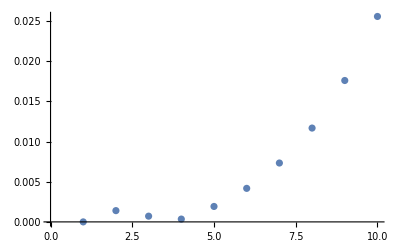

```mathematica
ListPlot[uerror]
```

### One corrector executed at each step

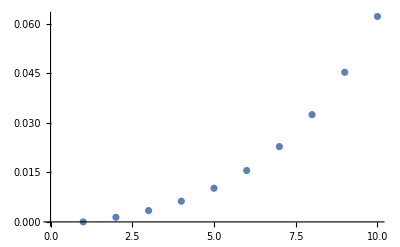

### At most three correctors executed at each step

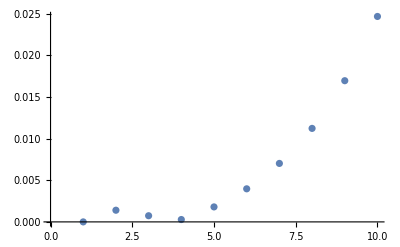

### At most ten correctors executed at each step

### 0 correctors: actual vs computed

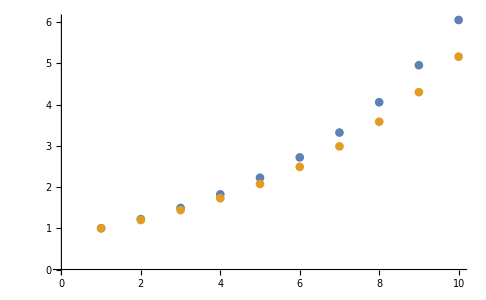

```mathematica
ListPlot[{uact, ucomp}]
```

### 1 corrector: actual vs computed

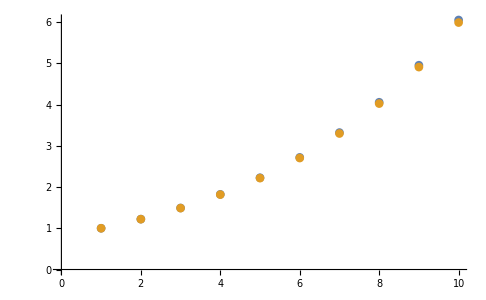

```mathematica
ListPlot[{uact, ucomp}]
```

### At most 3 correctors: actual vs computed

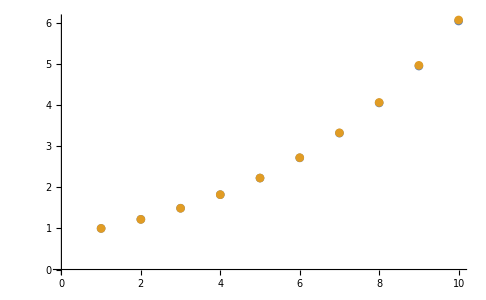

```mathematica
ListPlot[{uact, ucomp}]
```

### 11 correctors: actual vs computed

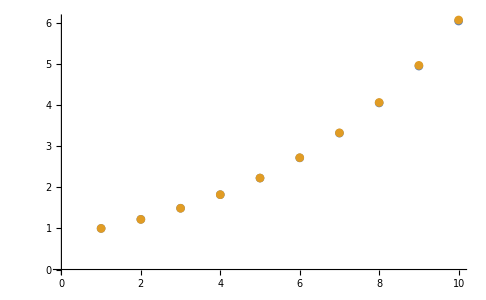

```mathematica
ListPlot[{uact, ucomp}]
```

# Forward Euler, Forward Euler with Corrector method

```mathematica
u0 = 1;
a=2;
x0=0;
dx = .1;
u[x_]:= E^x;
up[x_]:= a*x;
```

```mathematica
ucomp = {};
uact = {};
uerror = {};
For[i = 0, i ≤ 9, i++, 
(* compute and append actual value *)
act = u[a*i*dx];
AppendTo[uact,act];
(* append computed value *)
AppendTo[ucomp,u0];
(* compute and append error *)
err = Abs[act - u0];
AppendTo[uerror,err];
(*compute actual *)
u0 = u0 + up[u0]*dx;
];
Print["computed"]
ucomp
Print["actual"]
uact
Print["uerror"]
uerror
```

computed

{1,1.2,1.44,1.728,2.0736,2.48832,2.98598,3.58318,4.29982,5.15978}

actual

{1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965}

uerror

{0.,0.0214028,0.0518247,0.0941188,0.151941,0.229962,0.334133,0.472019,0.653215,0.889867}

```mathematica
ListPlot[uerror]
```

-Graphics-

```mathematica
(* CORRECTOR 
now we want the following:   

we use x0 and u0 to compute a value of the derivative up[u0], we can use up[u1] where we have just computed u1 to recalculate our estimate for up[u0]. 

set upcorrected = Avg(up[u0] and u[u1]). Then recompute u1.  

*)
```

```mathematica
u0 = 1;
a=2;
x0=0;
dx = .1;
u[x_]:= E^x;
up[x_]:= a*x;
```

```mathematica
ucomp = {};
uact = {};
For[i = 0, i ≤ 9, i++, 
(* compute and append actual value *)
act = u[a*i*dx];
AppendTo[uact,act];
(* append computed value *)
AppendTo[ucomp,u0];


(* f(x0,u0)  calculate the derivative *)
upprev =up[u0];

(* compute the next step*)
u1 = u0 + up[u0]*dx;

(* f(x1,u1)   calculate the derivative at the estimate for the next step *)
upnext =up[u1];

(* compute the corrector *)
upcorrector = (upprev + upnext)/2;

(* compute the new value *)

uc = u0 + upcorrector * dx;

Print["u1 step" ,i,"is", u1];
Print["uc step" ,i,"is", uc];
(*
UNCOMMENT THE LOOP FOR MULTIPLE ERROR CORRECTION. 
*)
For[j = 1, j ≤ 2, ++j,

If[Abs[u1 - uc]>.02,

Print["At step" ,i,"we execute the corrector logic again" ];
upnext = up[uc];
upcorrector = (upprev + upnext)/2;
uc = u0 + upcorrector * dx;

];
];



u0 = uc;
];
(* compute and append error *)
uerror = Abs[ucomp - uact];

Print["computed"]
ucomp
Print["actual"]
uact
Print["uerror"]
uerror
```

u1 step0is1.2

uc step0is1.22

u1 step1is1.464

uc step1is1.4884

At step1we execute the corrector logic again

At step1we execute the corrector logic again

u1 step2is1.7893

uc step2is1.81912

At step2we execute the corrector logic again

At step2we execute the corrector logic again

u1 step3is2.18688

uc step3is2.22333

At step3we execute the corrector logic again

At step3we execute the corrector logic again

u1 step4is2.67281

uc step4is2.71736

At step4we execute the corrector logic again

At step4we execute the corrector logic again

u1 step5is3.26671

uc step5is3.32115

At step5we execute the corrector logic again

At step5we execute the corrector logic again

u1 step6is3.99257

uc step6is4.05911

At step6we execute the corrector logic again

At step6we execute the corrector logic again

u1 step7is4.87972

uc step7is4.96105

At step7we execute the corrector logic again

At step7we execute the corrector logic again

u1 step8is5.96399

uc step8is6.06339

At step8we execute the corrector logic again

At step8we execute the corrector logic again

u1 step9is7.28919

uc step9is7.41068

At step9we execute the corrector logic again

At step9we execute the corrector logic again

computed

{1,1.22,1.49108,1.8224,2.22734,2.72226,3.32714,4.06643,4.96999,6.07433}

actual

{1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965}

uerror

{0.,0.00140276,0.000740698,0.000284064,0.00179985,0.00397407,0.00702424,0.011232,0.0169607,0.0246781}

```mathematica
ListPlot[uerror]
```

-Graphics-

### One corrector executed at each step

### One at most two correctors executed at each step